```mathematica
f[x_]:= (Cos[x])^4
```

```mathematica
L= π/2
```

π/2

```mathematica
2
```

2

```mathematica
a0:= 1/(2*L)∫_-L^L (f[x])ⅆx
```

```mathematica
a[n_]:=1/L∫_-L^L (f[x]*Cos[(n*x*π)/L])ⅆx
```

```mathematica
b[n_]:=1/L*∫_-L^L f[x]*Sin[(n*x*π)/L]ⅆx
```

```mathematica
f[x]
```

Cos[x]^4

```mathematica
a[5]
```

0

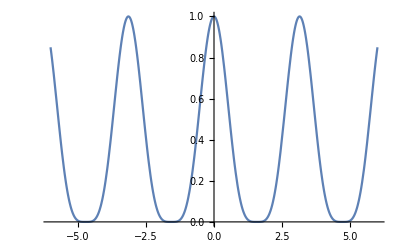

```mathematica
Plot[{f[x]},{x,-6,6}]
```

```mathematica
b[1]
```

0

```mathematica
g[x_]:= b[1]Sin[x]+b[2]Sin[2*x]+b[3]Sin[3*x]+b[4]Sin[4*x]+b[5]Sin[5*x]+b[6]Sin[6*x]+b[7]Sin[7*x]
```

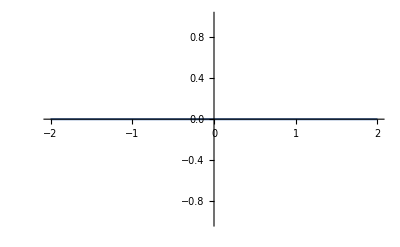

```mathematica
Plot[{g[x]},{x,-2,2}]
```

```mathematica
d3=a0+∑_(n=1)^20 (a[n]*Cos[(n*x*π)/L]+b[n]*Sin[(n*x*π)/L])
```

3/8+1/2 Cos[2 x]+1/8 Cos[4 x]

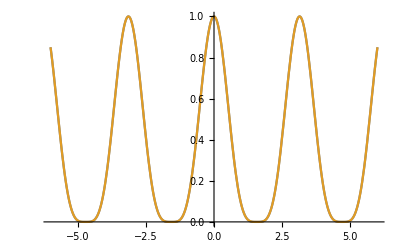

```mathematica
Plot[{d3, f[x]},{x,-6,6}]
```

```mathematica
br[n_] := 1/(2*L)∫_-L^L (f[x]*ⅇ^(-ⅈ*(n*π*x)/L))ⅆx
```

```mathematica
br[0]
```

3/8

```mathematica
br[2]
```

(2 ⅈ)/π

este intervalo es para la funcion x|x| de -2<x<2 y hay error en 0

```mathematica
p3=(∑_(n=-20)^-1 br[n]*ⅇ^(ⅈ*(n*π*x)/L))+(∑_(n=1)^20 br[n]*ⅇ^(ⅈ*(n*π*x)/L))
```

-(2 ⅈ ⅇ^(-4 ⅈ x))/π+(2 ⅈ ⅇ^(4 ⅈ x))/π-(ⅈ ⅇ^(-8 ⅈ x))/π+(ⅈ ⅇ^(8 ⅈ x))/π-(2 ⅈ ⅇ^(-12 ⅈ x))/(3 π)+(2 ⅈ ⅇ^(12 ⅈ x))/(3 π)-(ⅈ ⅇ^(-16 ⅈ x))/(2 π)+(ⅈ ⅇ^(16 ⅈ x))/(2 π)-(2 ⅈ ⅇ^(-20 ⅈ x))/(5 π)+(2 ⅈ ⅇ^(20 ⅈ x))/(5 π)-(ⅈ ⅇ^(-24 ⅈ x))/(3 π)+(ⅈ ⅇ^(24 ⅈ x))/(3 π)-(2 ⅈ ⅇ^(-28 ⅈ x))/(7 π)+(2 ⅈ ⅇ^(28 ⅈ x))/(7 π)-(ⅈ ⅇ^(-32 ⅈ x))/(4 π)+(ⅈ ⅇ^(32 ⅈ x))/(4 π)-(2 ⅈ ⅇ^(-36 ⅈ x))/(9 π)+(2 ⅈ ⅇ^(36 ⅈ x))/(9 π)-(ⅈ ⅇ^(-40 ⅈ x))/(5 π)+(ⅈ ⅇ^(40 ⅈ x))/(5 π)+(2 ⅇ^(-2 ⅈ x) (-8 ⅈ+2 ⅈ π^2))/π^3-(2 ⅇ^(2 ⅈ x) (-8 ⅈ+2 ⅈ π^2))/π^3+(2 ⅇ^(-6 ⅈ x) (-8 ⅈ+18 ⅈ π^2))/(27 π^3)-(2 ⅇ^(6 ⅈ x) (-8 ⅈ+18 ⅈ π^2))/(27 π^3)+(2 ⅇ^(-10 ⅈ x) (-8 ⅈ+50 ⅈ π^2))/(125 π^3)-(2 ⅇ^(10 ⅈ x) (-8 ⅈ+50 ⅈ π^2))/(125 π^3)+(2 ⅇ^(-14 ⅈ x) (-8 ⅈ+98 ⅈ π^2))/(343 π^3)-(2 ⅇ^(14 ⅈ x) (-8 ⅈ+98 ⅈ π^2))/(343 π^3)+(2 ⅇ^(-18 ⅈ x) (-8 ⅈ+162 ⅈ π^2))/(729 π^3)-(2 ⅇ^(18 ⅈ x) (-8 ⅈ+162 ⅈ π^2))/(729 π^3)+(2 ⅇ^(-22 ⅈ x) (-8 ⅈ+242 ⅈ π^2))/(1331 π^3)-(2 ⅇ^(22 ⅈ x) (-8 ⅈ+242 ⅈ π^2))/(1331 π^3)+(2 ⅇ^(-26 ⅈ x) (-8 ⅈ+338 ⅈ π^2))/(2197 π^3)-(2 ⅇ^(26 ⅈ x) (-8 ⅈ+338 ⅈ π^2))/(2197 π^3)+(2 ⅇ^(-30 ⅈ x) (-8 ⅈ+450 ⅈ π^2))/(3375 π^3)-(2 ⅇ^(30 ⅈ x) (-8 ⅈ+450 ⅈ π^2))/(3375 π^3)+(2 ⅇ^(-34 ⅈ x) (-8 ⅈ+578 ⅈ π^2))/(4913 π^3)-(2 ⅇ^(34 ⅈ x) (-8 ⅈ+578 ⅈ π^2))/(4913 π^3)+(2 ⅇ^(-38 ⅈ x) (-8 ⅈ+722 ⅈ π^2))/(6859 π^3)-(2 ⅇ^(38 ⅈ x) (-8 ⅈ+722 ⅈ π^2))/(6859 π^3)

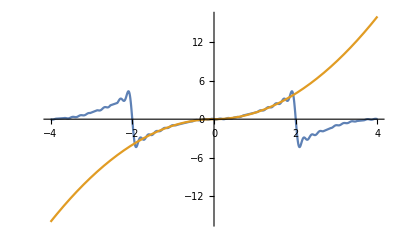

```mathematica
Plot[{Re[p3], f[x]},{x,-4,4}]
```

La sumatoria se divide porque hay un error en el cero, y en la grafica se debe colocar Re, para graficar la parte real.
si es par- reales
si es impar- imaginarios puros
si no es ninguno - imaginarios puros y reales

```mathematica
br[0]
```

3/8

sumatoria para la funcion cos(x)^4 con t=pi

```mathematica
p4=(∑_(n=-1)^2 br[n]*ⅇ^(ⅈ*(n*π*x)/L))
```

3/8+1/4 ⅇ^(-2 ⅈ x)+1/4 ⅇ^(2 ⅈ x)+1/16 ⅇ^(4 ⅈ x)

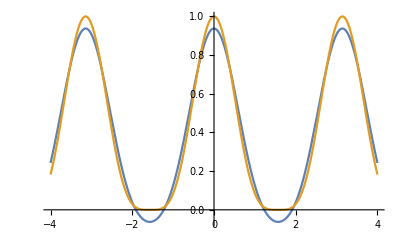

```mathematica
Plot[{Re[p4], f[x]},{x,-4,4}]
```